```mathematica
Export["~/documents/thesis/figures/ripple/ang_abs_factor_Bragg.dat", Table[{qz,A[th[qz],th[qz]]}, {qz,0.05,1.0,0.001}]]
```

~/documents/thesis/figures/ripple/ang_abs_factor_Bragg.dat

```mathematica
Export["~/MyDocuments/work/thesis/figures/ripple/analysis/abs_integrand.dat", Table[{ω,A[ω*π/180,0.58*π/180]}, {ω,0.01,1.15,0.01}]]
```

~/MyDocuments/work/thesis/figures/ripple/analysis/abs_integrand.dat

```mathematica
Export["~/documents/thesis/figures/ripple/abs_factor.dat", Table[{qz,AA[th[qz]]}, {qz,0.05,1.0,0.001}]]
```

~/documents/thesis/figures/ripple/abs_factor.dat

```mathematica
A[0.2*π/180,1.1*π/180]
```

0.579525

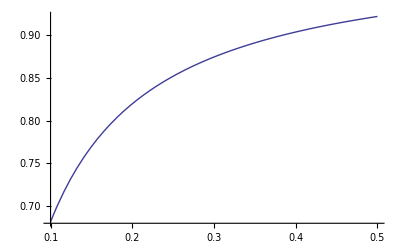

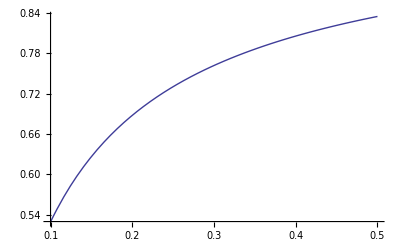

```mathematica
g[ω_,θ_]:=1/Sin[ω]+1/Sin[2θ-ω]
A[ω_,θ_]:=μ/t(1-Exp[-t/μ g[ω,θ]])/g[ω,θ]

th[qz_]:=λ qz/(4π)
w=0.6*π/180;(*rad*)
λ=1.175;(*Angstrom*)
μ=2600;(*um*)
t=10;(*um*)
(*Plot[A[θ,θ],{θ,0.6Degree,3Degree}]
Plot[A[th[qz],th[qz]],{qz,0,0.5}]*)
AA[θ_]:=1/(2θ)NIntegrate[A[ω,θ],{ω,0,2θ}]
Plot[A[th[qz],th[qz]],{qz,0.1,0.5}]
Plot[AA[th[qz]],{qz,0.1,0.5}]
```

```mathematica
Export["/home/unkokusei/MyDocuments/work/thesis/figures/ripple/abs_factor.dat", Table[{i,i^2}, {i, 10}]]
```

```mathematica
Table[i,{i,0,2,0.2}]
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.}

```mathematica
0.5 Degree
```

0.00872665

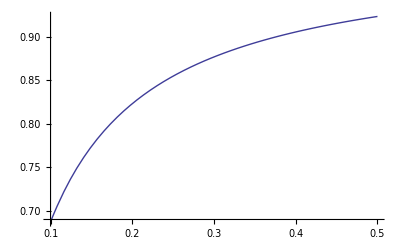

```mathematica
YL[θ_]:=(1-Exp[(-2Lz Num)/(μ Sin[θ])])/(1-Exp[(-2Lz)/(μ Sin[θ])])
Num=50;
μ=2600;
Lz=0.2;
Plot[YL[th[qz]]/Num,{qz,0.1,0.5}]
```